| Estimate | Standard Error | t-Statistic | P-Value
μ | 90.6604 | 0.0731377 | 1239.59 | 1.34671×10^-101
σ | 3.65621 | 0.0798007 | 45.8168 | 9.0101×10^-39
k | 16956.2 | 302.98 | 55.9647 | 1.56709×10^-42

| Estimate | Standard Error | t-Statistic | P-Value
μ | 232.226 | 0.273082 | 850.388 | 6.11702×10^-102
σ | 7.9519 | 0.277505 | 28.655 | 7.63693×10^-32
k | 87051.7 | 2603.05 | 33.4423 | 6.50732×10^-35

Cs137-1-no-bg

/Users/soerenlink/Projekte/fp-Gamma-Radiation/mathematica/../data/Cs137-1-no-bg-calibrated.txt

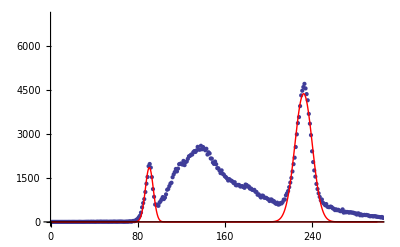

```mathematica
(*Clear unused stuff*)
Clear[ Filename, Filepath, rawBackground, rawData, BackgroundTime, DataTime, removeBackground];

type = "Na2";

(*Specify folder structure and filenames*)
Filename = If[type=="Na","Na22-no-bg", "Cs137-1-no-bg"];
Filepath = NotebookDirectory[]<>"../data/";

(*Import raw data from .Spe files*)
rawData = Import[Filepath<> Filename <>".txt", "Table"];
cutData = rawData;

xraypeak = Take[cutData, If[type=="Na", {130,160}, {50,96}]];
gammapeak = Take[cutData, If[type=="Na", {200,250}, {200,250}]];

model[x_] =k*Exp[-1/2 ((x-μ)/σ)^2]/(σ √(2 π));

xrayfitModel=NonlinearModelFit[xraypeak, model[x], {{μ, If[type=="Na",140, 90]}, {σ, 4}, {k, 20000}}, x];
gammafitModel=NonlinearModelFit[gammapeak, model[x], {{μ, 220}, {σ, 8}, {k, 90000}}, x];

xrayfitModel["ParameterTable"]
gammafitModel["ParameterTable"]

xrayfit = xrayfitModel["BestFitParameters"];
gammafit = gammafitModel["BestFitParameters"];
xrayTeX = model[x]/.xrayfit;
gammaTeX = model[x]/.gammafit;

ExportString[xrayTeX, "TeX"];
ExportString[gammaTeX, "TeX"];

(* Energy Calibration *)
lit1 =If[type=="Na",511, 32.9];
lit2 =If[type=="Na",1275, 661.66];
DataSet ={{Last[First[xrayfit]], lit1}, {Last[First[gammafit]], lit2}};
calibration=LinearModelFit[DataSet,x,x]

exportName ="Cs137-1-no-bg"
dataToCalibrate = Import[Filepath<> exportName <>".txt", "Table"];
calibratedDate = Select[{calibration[First[#]], Last[#]}&/@dataToCalibrate,First[#]≥0&];
(*Export[Filepath<> exportName <>"-calibrated.txt", calibratedDate, "Table"];*)


Show[{ListPlot[cutData, PlotRange->{{0,300}, {0, 7000}}], Plot[ model[x]/.xrayfit,  {x,0,400}, PlotStyle->Red, PlotRange->{{0,300}, {0, 7000}}],Plot[ model[x]/.gammafit,  {x,0,300}, PlotStyle->Red, PlotRange->{{0,300}, {0, 7000}}]}]
```